# Quantum Teleportation

## Implementation quantum teleportation using the Q3 Application

## Example 1. Input State is Chosen Randomly

```mathematica
Quit[]
```

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

Bob chooses randomly the state to teleport to Alice, and prepare the third Qubit S[3,None] in it.

```mathematica
in=Basis[S[3]].Normalize@RandomReal[{-1,1},2]
```

0.946856 ␣-0.321657 1_S_3

Check the normalization of the state.

```mathematica
Dagger[in]**in//Chop
```

1.

Here is the quantum circuit of teleportation.

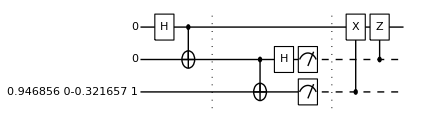

```mathematica
qc=QuantumCircuit[
in,LogicalForm[Ket[],S@{1,2}],
S[1,6],CNOT[S[1],S[2]],"Separator","Spacer",
CNOT[S[2],S[3]],
S[2,6],{Measurement[S[2]],Measurement[S[3]]},"Separator",
ControlledU[S[3],S[1,1]],
ControlledU[S[2],S[1,3]]
]
```

Convert the quantum circuit  to an expression by means of either ExpressionFor or Matrix (usually faster).

```mathematica
outAll=ExpressionFor[qc]//Simplify
```

-0.321657 1_S_11_S_3+0.946856 1_S_3

Let us examine the state in Alice’s qubit (S[1,None]).

```mathematica
out=Last@KetFactor[outAll,S[{2,3}]]//Simplify;
out//LogicalForm
```

0.946856 0_S_1-0.321657 1_S_1

You can see the state is the same as the input state. In case, there is irrelevant overall phase factor, let us check the fidelity.

```mathematica
Fidelity[Matrix@in,Matrix@out]
```

1.

As the quantum teleportation is deterministic, Bob’s Bell measurement result does not matter. For the heuristic purposes, let us take a look at Bob’s measurement statistics.

```mathematica
val=Table[
out=ExpressionFor[qc]//Simplify;
Readout[out,S[{2,3}]],
{100}
];
Histogram3D[val]
```

-Graphics3D-

## Example 2. Input State is Prepared by Rotations

```mathematica
Quit[]
```

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

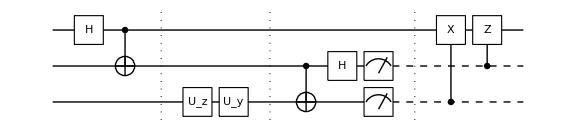

```mathematica
Rz=Rotation[Pi/3,S[3,3],Label->"R"];
Ry=Rotation[Pi/6,S[3,2],Label->Superscript["R",′]];
qc=QuantumCircuit[
Ket[],
S[1,6],CNOT[S[1],S[2]],"Separator",
Rz,Ry,"Separator",
CNOT[S[2],S[3]],
S[2,6],{Measurement[S[2]],Measurement[S[3]]},"Separator",
ControlledU[S[3],S[1,1]],
ControlledU[S[2],S[1,3]]
];
gr=Graphics[qc,ImageSize->Large]
```

Converting the quantum circuit to a explicit expression,

```mathematica
out=Elaborate[qc]//Simplify
w=KetFactor[out,S[{2,3}]]//Simplify;
w//LogicalForm
v=Rz**Ry**Ket[]//Simplify;
LogicalForm[v]
```

((-1-ⅈ) ((-2+ⅈ)+√3) 1_S_11_S_3+(1-ⅈ) ((2+ⅈ)+√3) 1_S_3)/(4 √2)

0_S_21_S_3⊗(((1/4-ⅈ/4) (((2+ⅈ)+√3) 0_S_1+((1+2 ⅈ)-ⅈ √3) 1_S_1))/(√2))

((1/4-ⅈ/4) (((2+ⅈ)+√3) 0_S_3+((2+ⅈ)-√3) 1_S_3))/(√2)

```mathematica
val=Table[
out=Elaborate[qc]//Simplify;
Readout[out,S[{2,3}]],
{100}
];
Histogram3D[val]
```

-Graphics3D-

Explicitly constructing the expression,

```mathematica
vec=Multiply[
ControlledU[S[2],S[1,3]],
ControlledU[S[3],S[1,1]],
Measurement[Measurement[
Garner@Multiply[S[2,6],
CNOT[S[2],S[3]],
Rz,Ry,
CNOT[S[1],S[2]],
S[1,6],
Ket[S[{1,2,3}]->1]],S[3]],S[2]]]//Simplify;
KetFactor[vec,S[{2,3}]]
orig=Rz**Ry**Ket[]//Simplify
```

0_S_20_S_3⊗(((1/4+ⅈ/4) ((2-ⅈ) ␣+√3 ␣+(2-ⅈ) 1_S_1-√3 1_S_1))/(√2))

((1/4-ⅈ/4) (((2+ⅈ)+√3) ␣+((2+ⅈ)-√3) 1_S_3))/(√2)